# Lab 1

## Michael Curry 1/24/2020

## List out the first 48 Lucas Numbers

WolframAlphaQueryParseResults

{1,3,4,7,11,18,29,47,76,123,199,322,521,843,1364,2207,3571,5778,9349,15127,24476,39603,64079,103682,167761,271443,439204,710647,1149851,1860498,3010349,4870847,7881196,12752043,20633239,33385282,54018521,87403803,141422324,228826127,370248451,599074578,969323029,1568397607,2537720636,4106118243,6643838879,10749957122}

## Verify that their digital root values follow a periodic pattern with length 24.

```mathematica
digitalSum[k_Integer]:=Total@IntegerDigits[k]
digitalRoot[k_Integer]:=FixedPoint[digitalSum,k]
Table[digitalRoot[LucasL[i]],{i,48}]
```

{1,3,4,7,2,9,2,2,4,6,1,7,8,6,5,2,7,9,7,7,5,3,8,2,1,3,4,7,2,9,2,2,4,6,1,7,8,6,5,2,7,9,7,7,5,3,8,2}

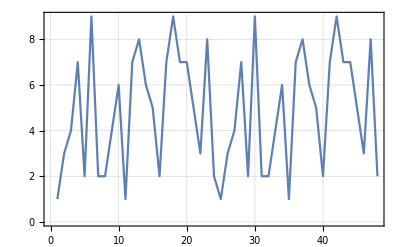

```mathematica
ListLinePlot[{1,3,4,7,2,9,2,2,4,6,1,7,8,6,5,2,7,9,7,7,5,3,8,2,1,3,4,7,2,9,2,2,4,6,1,7,8,6,5,2,7,9,7,7,5,3,8,2},PlotTheme->"Detailed"]
```

## Find the numerical values in days for the following astronomical variables: Eclipse year (also known as Draconic year) Sidereal Year 13 lunar months

WolframAlphaQueryParseResults

eclipse years

```mathematica
UnitConvert[Quantity[None,"DraconicYears"],"Days"]
```

346.620075883 days

WolframAlphaQueryParseResults

sidereal years

```mathematica
UnitConvert[Quantity[None,"SiderealYears"],"Days"]
```

365.256360417 days

WolframAlphaQueryParseResults

13 lunar months

```mathematica
UnitConvert[Quantity[13,"LunarMonths"],"Days"]
```

```mathematica
Quantity[383.8976435185185185185`7.9596278051226905, "Days"]
```

## Generate numerical values for the following variables eclipseyear = (L6 + 1/ϕ)^2 siderealyear = (L6 + 1/ϕ)(L6 + ϕ) lunations13 = (L6 + 1/ϕ)(L6 + ϕ^2)

```mathematica
eclipseyear = N[(LucasL[6]+(1/GoldenRatio))^2]
```

346.631

```mathematica
siderealyear = N[((LucasL[6] + (1/GoldenRatio)) * (LucasL[6]+GoldenRatio))]
```

365.249

```mathematica
lunation13 = N[((LucasL[6] + (1/GoldenRatio)) *(LucasL[6] + GoldenRatio^2))]
```

383.867

## Compare your generated values (interpreting them as measured in number of days) to the observed values and report the relative error (in percents) in each case.

```mathematica
((eclipseyear - UnitConvert[Quantity[None,"DraconicYears"],"Days"])/ N[UnitConvert[Quantity[None,"DraconicYears"],"Days"]])*100
```

(346.631+-346.620075883 days) (0.2885 per day)

```mathematica
((siderealyear - UnitConvert[Quantity[None,"SiderealYears"],"Days"])/ N[UnitConvert[Quantity[None,"SiderealYears"],"Days"]])*100
```

(365.249+-365.256360417 days) (0.27378 per day)

```mathematica
((lunation13 - UnitConvert[Quantity[13,"LunarMonths"],"Days"])/ N[UnitConvert[Quantity[13,"LunarMonths"],"Days"]])*100
```

(383.867+-383.8976 days) (0.260486 per day)